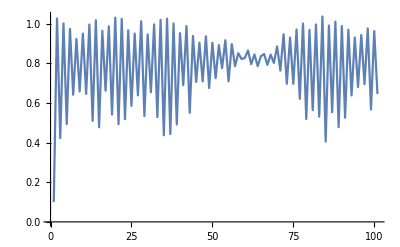

```mathematica
data=NestList[Chop[Cos[#^3]]+RandomReal[{-0.05,0.05}]&,0.1,100];
ListLinePlot[data,PlotRange->All]
```

```mathematica
data//Mean
```

0.778098

```mathematica
data//StandardDeviation
```

0.206065

```mathematica
data//AutocorrelationTest
```

1.45412×10^-89

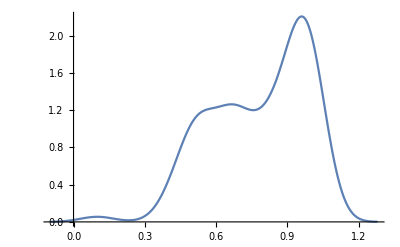

```mathematica
data//SmoothHistogram
```

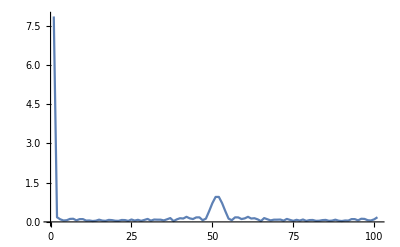

```mathematica
ListLinePlot[data//Fourier//Abs,PlotRange->All]
```

```mathematica
data=FinancialData["GOOG","Jan. 1, 2000"];
```

```mathematica
data=Last/@data;
```

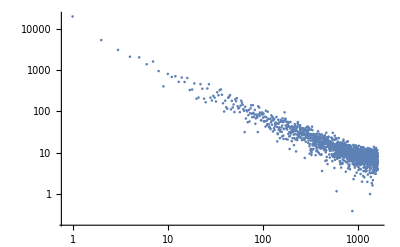

```mathematica
ListLogLogPlot[(data//Fourier//Abs)[[;;1600]],PlotRange->All]
```

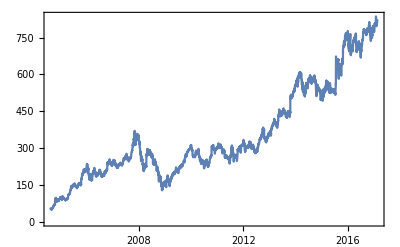

```mathematica
DateListPlot[data]
```